```mathematica
例：乘方运算
```

```mathematica
2^20
```

```mathematica
N[Pi,123]
```

```mathematica
例：因式分解
```

```mathematica
Factor[x^3-12x^2-145x+1716]
```

```mathematica
例：多项式展开
```

```mathematica
Expand[(x-3)(y^2-x+6)]
```

```mathematica
例：计算 391,561,357的最大公约数
```

```mathematica
GCD[391,561,357]
```

```mathematica
例：计算 最小公倍数
```

```mathematica
LCM[21,29,35]
```

```mathematica
Solve[{3x-2y==5,x+y==5},{x,y}]
```

```mathematica
Sum[1/k^2, {k, 1, Infinity}]
```

```mathematica
D[x^2/Sin[x],x]
```

```mathematica
D[x^2/Sin[x],{x,10}]
```

```mathematica
Integrate[12!Cos[x]^5 Sin[x+y]^3,x,y]
```

```mathematica
AA={{1,2,3,4},{3,2,5,6},{1,2,-1,2},{0,2,5,7}};
AB={{7,6,5,4},{8,5,3,2},{9,6,1,8},{0,-3,-4,5}};
AC={{3,1,2,0},{4,5,0,8},{6,7,1,9},{7,8,2,3}};
AA.AB+AC(*矩阵运算如此简单!*)
```

```mathematica
MatrixForm[%]
```

```mathematica
Eigensystem[{{0,1},{1,1}}]
```

```mathematica
AA={{Sin[x]+x^2,Cos[y]-x,Exp[x]-x^3},{x Sin[x]+x^2,Cos[y]+x^3,Exp[x]+Abs[x]},{Cos[x]+Sin[x],Cos[y]-x,Exp[x]+Sqrt[x]}};
MatrixForm[AA]
MatrixForm[AA.Transpose[AA]](* 9 3 4 = 108 *)
```

```mathematica
Plot[Sin[x/2],{x,-20,20}]
Plot[Sin[x],{x,-20,20}]
Plot[Sin[2x],{x,-20,20}]
Plot[Sin[x/2]+Sin[2x]+Sin[x],{x,-20,20}]
```

```mathematica
ParametricPlot[{Sin[0.99t]-0.7*Cos[3.01t],Cos[1.01t]+0.1Sin[15.03t]},{t,-150,150},Axes->None]
```

```mathematica
例：绘制单叶双曲面 x^2/4+y^2/3-z^2/2==1
```

```mathematica
{xa,yb,zc}={4,3,2};
ContourPlot3D[x^2/xa+y^2/yb-z^2/zc==1,{x,-xa,xa},{y,-yb,yb},{z,-zc,zc},Axes->False,Boxed->False]
```

```mathematica
Plot3D[Sin[x  y],{x,-4,4},{y,-4,4}]
```

```mathematica
例：用ParametricPlot3D语句绘制Möbius带
```

```mathematica
ParametricPlot3D[{Cos[t](3+r*Cos[t/2]),Sin[t](3+r*Cos[t/2]),r*Sin[t/2]},{r,-1,1},{t,0,2Pi},Axes->False,Boxed->False]
```

```mathematica
例：直纹面生成单叶双曲面.
```

```mathematica
Speak[由直纹面动态生成单叶双曲面]
```

```mathematica
u={-1.5,1.5};
Animate[Graphics3D[Table[{Hue[s/2],Line[{{Cos[t]-Sin[t],Cos[t]+Sin[t],1},{Cos[t]+Sin[t],Sin[t]-Cos[t],-1}}]},{t,0,s,Pi/27}],Boxed->False,PlotRange->{u,u,u}],{s,0,2Pi,Pi/27}]
```

```mathematica
例：演奏贝多芬第五交响乐的第一个音节
```

```mathematica
Speak[演奏贝多芬第五交响乐的第一个音节 ]
```

```mathematica
Sound[{SoundNote["G"],SoundNote["G"],SoundNote["G"],SoundNote["Eb",4]},1.5]
```

```mathematica
《来生缘》
```

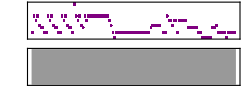

```mathematica
Sound[{SoundNote[-3,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-3,0.2],

SoundNote[-3,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-3,0.2],SoundNote[9,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[4,0.2],SoundNote[2,0.2],

SoundNote[4,2.4],SoundNote[2,0.2],SoundNote[0,0.2],SoundNote[-3,0.2],SoundNote[-5,0.2],

SoundNote[-3,2.75],

SoundNote[-3,0.8],SoundNote[-3,0.4],SoundNote[-1,0.2],SoundNote[0,1],(*寻寻觅觅*)

SoundNote[None,0.25],SoundNote[-3,0.4],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[2,0.2],SoundNote[0,0.2],SoundNote[2,0.4],SoundNote[-3,0.2],SoundNote[2,1],(*在无声无息中消失*)

SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-1,0.4],SoundNote[-3,0.4],SoundNote[-5,0.0],SoundNote[-5,0.6],(*总是找不到回忆*)

SoundNote[-5,0.2],SoundNote[-5,0.4],SoundNote[-3,0],SoundNote[-1,0.4],SoundNote[0,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[-3,0.4],SoundNote[-5,0.2],SoundNote[-3,1],SoundNote[None,0.3]}]
```